# 1. DN - Računalniška orodja v matematiki

#### 1. Analiza z mathematico

Točke od a do j rešite točno in tudi numerično.

a. Definirajte funkcijo .

```mathematica
f[x_]:=Power[E, x+3]/(100x+2)
f[x]
```

ⅇ^(3+x)/(2+100 x)

b. Izračunajte definicijsko območje funkcije .

```mathematica
FunctionDomain[f[x], x]
```

```mathematica
x<-1/50||x>-1/50
N[FunctionDomain[f[x], x]]
```

x<-1/50||x>-1/50

x<-0.02||x>-0.02

c. Izračunajte limite funkcije  na robovih definicijskega območja.

```mathematica
Limit[f[x], x->-1/50, Direction->-1]
```

∞

```mathematica
Limit[f[x], x->-1/50, Direction->1]
```

-∞

d. Izračunajte odvod funkcije .

```mathematica
f'[x] //FullSimplify
```

(ⅇ^(3+x) (-49+50 x))/(2 (1+50 x)^2)

e. Izračunajte lokalne ekstreme funkcije .

```mathematica
FindMaximum[f[x], x]
```

{3.512388747422667570185238117131315641`15.954589770191005*^329846514457743,{x→7.595×10^14}}

```mathematica
N[FindMaximum[f[x], x]]
```

General::ovfl: Overflow occurred in computation.

FindMaximum::nrnum: The function value Overflow[] is not a real number at {x} = {8.3545×10^15}.

{3.512388747422667570185238117131315641`15.954589770191005*^329846514457743,{x→7.595×10^14}}

```mathematica
FindMinimum[f[x], x]
```

{0.53517,{x→0.98}}

f. Izračunajte intervale naraščanja in padanja funkcije .

```mathematica
Reduce[f'[x] > 0, x]
```

x>49/50

```mathematica
N[Reduce[f'[x] > 0, x]]
```

x>0.98

g. Narišite graf funkcije  na intervalu [-5, 5].

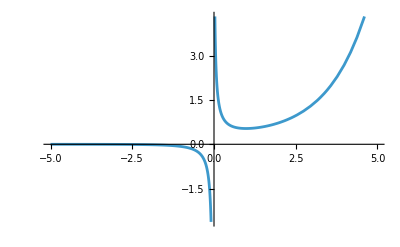

```mathematica
Plot[f[x], {x, -5, 5}]
```

h. Določite zalogo vrednosti funkcije .

```mathematica
FunctionRange[f[x], x, y]
```

y<0||y≥ⅇ^(199/50)/100

```mathematica
N[FunctionRange[f[x], x, y]]
```

y<0.||y≥0.53517

i. Izračunajte nedoločeni integral funkcije .

```mathematica
Integrate[f[x], x] // FullSimplify
```

1/100 ⅇ^(149/50) ExpIntegralEi[1/50+x]

j. Na 3 decimalke natančno izračunajte volumen vrtenine , ki jo dobimo, če graf funkcije  zavrtimo okoli  osi na intervalu [0.5, 2]. Vrtenino tudi narišite.

```mathematica
Round[Pi * Integrate[f[x]^2, {x, 0.5, 2}], 0.001]
```

1.665

#### 2. Splošno o mathematici

a. Pobrišite vrednost vseh spremenljivk, ki ste jih uporabili v prejšnji nalogi.

```mathematica
ClearAll[f]
```

b. Definirajte funkcijo  in izračunajte njeno vrednost v vseh celih številih med 1 in 100.

```mathematica
g[x_] := (1+Power[x, 2.1])/(3+x)
```

```mathematica
tab := Table[g[x], {x, 1, 100}]
```

```mathematica
tab
```

{0.5,1.05742,1.84085,2.76845,3.79568,4.89604,6.05259,7.25393,8.49202,9.76096,11.0563,12.3747,13.7134,15.0702,16.4433,17.8313,19.2328,20.6469,22.0727,23.5093,24.956,26.4123,27.8776,29.3514,30.8333,32.3228,33.8198,35.3238,36.8345,38.3516,39.875,41.4044,42.9396,44.4803,46.0265,47.5778,49.1343,50.6956,52.2618,53.8326,55.4079,56.9876,58.5716,60.1598,61.7521,63.3483,64.9485,66.5525,68.1602,69.7716,71.3865,73.005,74.6269,76.2521,77.8807,79.5125,81.1475,82.7856,84.4268,86.0711,87.7183,89.3684,91.0214,92.6772,94.3359,95.9972,97.6613,99.3281,100.997,102.669,104.344,106.021,107.7,109.382,111.067,112.754,114.443,116.134,117.828,119.524,121.222,122.923,124.625,126.33,128.037,129.746,131.457,133.171,134.886,136.603,138.322,140.044,141.767,143.492,145.219,146.948,148.679,150.412,152.146,153.883}

c.  Iz seznama dobljenega v nalogi b. izberite zgolj tiste vrednosti, ki imajo na mestu enic praštevilo. Pomagajte si s _?PrimeQ in MemberQ.

```mathematica
primeNumebers = {2, 3, 5, 7}
```

{2,3,5,7}

```mathematica
tab2=Select[tab, MemberQ[primeNumebers, Mod[Floor[#], 10]]&]
```

{2.76845,3.79568,7.25393,12.3747,13.7134,15.0702,17.8313,22.0727,23.5093,27.8776,32.3228,33.8198,35.3238,42.9396,47.5778,52.2618,53.8326,55.4079,63.3483,73.005,77.8807,82.7856,87.7183,92.6772,95.9972,97.6613,102.669,107.7,112.754,117.828,122.923,133.171,143.492,145.219,152.146,153.883}

d. Definirajte anonimno funkcijo, ki kvadrira število in mu prišteje 1 in jo uporabite na zgoraj dobljenem seznamu.

```mathematica
tab3 = Map[Function[x, x^2+1], tab2]
```

{8.66433,15.4072,53.6195,154.134,189.057,228.11,318.954,488.203,553.686,778.158,1045.77,1144.78,1248.77,1844.81,2264.65,2732.29,2898.95,3071.03,4014.01,5330.73,6066.4,6854.46,7695.49,8590.07,9216.47,9538.73,10542.,11600.4,12714.4,13884.4,15111.,17735.4,20591.,21089.6,23149.5,23680.9}

e. Seznam iz prejšnje naloge zaokrožite navzdol in seštejte vsa tista števila, ki so deliva s 3.

```mathematica
zaokrozen = Map[Round, tab3]
```

{9,15,54,154,189,228,319,488,554,778,1046,1145,1249,1845,2265,2732,2899,3071,4014,5331,6066,6854,7695,8590,9216,9539,10542,11600,12714,13884,15111,17735,20591,21090,23150,23681}

```mathematica
Total[Select[zaokrozen, Divisible[#, 3]&]]
```

110268

#### 3. Prepisovalna pravila

```mathematica
Clear[x, y, izraz]
izraz = x^2 + 2x + 1
```

1+2 x+x^2

a. Definirajte prepisovalno pravilo, ki  v izrazu vse pojavitve x zamenja z y + 1.

```mathematica
izraz /. x->y+1
```

1+2 (1+y)+(1+y)^2

b. Z uporabo prepisovalnih pravil izračunajte vrednost izraza za  x = 2

```mathematica
izraz /. x->2
```

9

c. Definirajte funkcija  in s pomočjo prepisovalnih pravil zamenjajte vse pojavitve  v

```mathematica
f[x_]:=x^5-4x^3+x^2+3x-2
```

```mathematica
f[x] /. x^n_ -> x^(n-1)
```

-2+4 x-4 x^2+x^4

d. Prepisovalno pravilo iz naloge c uporabite na funkciji ,  kolikokrat gre.

```mathematica
g[x_]:=x^2025
```

```mathematica
g[x] //. x^n_ -> x^(n-1)
```

x

e. Definiraj prepisovalna pravila, s pomočjo katerih lahko izračunate poljuben člen fibonaccijevega zaporedja, z začetkom `Fib[10]`

```mathematica
fib[n_]:=Last[NestList[{#[[2]], #[[1]] + #[[2]]} &, {0, 1}, n-1][[n-1]]]
```

```mathematica
fib[10]
```

34